# Prepare

```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

```mathematica
Get["../../neupackage/mma/neutrino.wl"]
```

```mathematica
Get["../../neupackage/mma/neumat.wl"]
```

```mathematica
plotstylecolorList={Brown,Gray,Purple,Orange,Red,Blue}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Parameters

```mathematica
endpoint=1000000;
deltamsquare13=2.6*10^(-15);(*MeV^2*)
energy10=10;(*Energy in units of MeV*)
energy20=20;(*Energy in units of MeV*)
?OmegaVacuum
omegaV=OmegaVacuum[energy10,deltamsquare13](*MeV*)(*deltamsquare13/(2 energy20)(*MeV*)*)(*For 10 MeV neutrinos*)
thetaV=ArcSin[√0.093]/2
```

Takes [energy_,deltam2_] as parameters and calculates ω_v. Should becareful about units.

1.3×10^-16

0.154948

```mathematica
energy20=20;(*Energy in units of MeV*)
```

```mathematica
fraction=1(*0.99*)
lambdaN=fraction*Cos[2thetaV]omegaV (*MeV*)
```

1

1.23808×10^-16

```mathematica
thetamVN=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2,Pi];
```

```mathematica
omegaVKK=OmegaVacuum[energy20,deltamsquare13](*MeV*)(*deltamsquare13/(2 energy20)(*MeV*)*)
lambdaNKK=0.5*Cos[2thetaV]omegaVKK (*MeV*)
omegaMKK=OmegaMatter2[lambdaNKK,thetaV,omegaVKK](*MeV*)
thetamV=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaNKK/omegaVKK)^2)]/2,Pi]
```

6.5×10^-17

3.09519×10^-17

3.67552×10^-17

0.198931

```mathematica
secondfrac=90;
onekListKK={1};
twokListKK={1,1/secondfrac};
oneaListKK=(*{0.1};*){0.02(MeVInverse2km[2Pi/(omegaMKK onekListKK[[1]])]/1500)^(5/3)};
twoaListKK=(*{0.1,0.1};*){0.02(MeVInverse2km[2Pi/(omegaMKK twokListKK[[1]])]/1500)^(5/3),0.02(MeVInverse2km[2Pi/(omegaMKK twokListKK[[2]])]/1500)^(5/3)};
(*{oneaListKK[[1]],10^(-5)}*)
onephiListKK={0};
twophiListKK={0,0};

endpointNReconstruct=960000
```

960000

```mathematica
twoaListKK
```

{0.0000357347,0.0645894}

```mathematica
Part[qValueOrderdList[listNGenerator[1,10],onekListKK,oneaListKK,onephiListKK,thetamV],1;;10]
Grid@%
```

{{{1},0.},{{-1},288905.},{{2},8.76971×10^9},{{-2},2.63091×10^10},{{3},2.12963×10^15},{{-3},4.25927×10^15},{{4},5.81805×10^20},{{-4},9.69676×10^20},{{5},1.88381×10^26},{{-5},2.82571×10^26}}

{1} | 0.
{-1} | 288905.
{2} | 8.76971×10^9
{-2} | 2.63091×10^10
{3} | 2.12963×10^15
{-3} | 4.25927×10^15
{4} | 5.81805×10^20
{-4} | 9.69676×10^20
{5} | 1.88381×10^26
{-5} | 2.82571×10^26

```mathematica
destructionQOrder=Part[qValueOrderdList[listNGenerator[2,10],twokListKK,twoaListKK,twophiListKK,thetamV],1;;10]
Grid@%
```

{{{1,0},0.},{{0,4},128.051},{{0,5},132.437},{{0,-4},139.963},{{0,-5},148.017},{{0,6},195.456},{{0,-6},223.378},{{0,3},237.155},{{0,-3},253.511},{{0,7},370.226}}

{1,0} | 0.
{0,4} | 128.051
{0,5} | 132.437
{0,-4} | 139.963
{0,-5} | 148.017
{0,6} | 195.456
{0,-6} | 223.378
{0,3} | 237.155
{0,-3} | 253.511
{0,7} | 370.226

```mathematica
Table[
{First@destructionQOrder[[n]],widthNList[First@destructionQOrder[[n]],twokListKK,twoaListKK,twophiListKK,thetamV]},{n,1,Length@destructionQOrder}]
Grid@%
```

{{{1,0},3.83423×10^-7},{{0,4},0.00746228},{{0,5},0.0071313},{{0,-4},0.00746228},{{0,-5},0.0071313},{{0,6},0.00477517},{{0,-6},0.00477517},{{0,3},0.00407609},{{0,-3},0.00407609},{{0,7},0.00249097}}

{1,0} | 3.83423×10^-7
{0,4} | 0.00746228
{0,5} | 0.0071313
{0,-4} | 0.00746228
{0,-5} | 0.0071313
{0,6} | 0.00477517
{0,-6} | 0.00477517
{0,3} | 0.00407609
{0,-3} | 0.00407609
{0,7} | 0.00249097

```mathematica
Table[
{First@destructionQOrder[[n]],MeVInverse2km[2Pi/(omegaMKK*widthNList[First@destructionQOrder[[n]],twokListKK,twoaListKK,twophiListKK,thetamV])]},{n,1,Length@destructionQOrder}]
Grid@%
```

{{{1,0},8.78313×10^7},{{0,4},4512.9},{{0,5},4722.36},{{0,-4},4512.9},{{0,-5},4722.36},{{0,6},7052.43},{{0,-6},7052.43},{{0,3},8261.97},{{0,-3},8261.97},{{0,7},13519.5}}

{1,0} | 8.78313×10^7
{0,4} | 4512.9
{0,5} | 4722.36
{0,-4} | 4512.9
{0,-5} | 4722.36
{0,6} | 7052.43
{0,-6} | 7052.43
{0,3} | 8261.97
{0,-3} | 8261.97
{0,7} | 13519.5

```mathematica
Table[
{First@destructionQOrder[[n]],bNList[First@destructionQOrder[[n]],twokListKK,twoaListKK,twophiListKK,thetamV]},{n,1,Length@destructionQOrder}];
Grid@%
```

{1,0} | 0.-3.83423×10^-7 ⅈ
{0,4} | -0.00746228
{0,5} | 0.+0.0071313 ⅈ
{0,-4} | 0.00746228
{0,-5} | 0.-0.0071313 ⅈ
{0,6} | 0.00477517
{0,-6} | -0.00477517
{0,3} | 0.-0.00407609 ⅈ
{0,-3} | 0.+0.00407609 ⅈ
{0,7} | 0.-0.00249097 ⅈ

```mathematica
widthNList[{1,0},{1,1/7000},twoaListKK3,twophiListKK,thetamV]
twoaListKK
```

MapThread::mptd: Object twoaListKK3 at position {2, 3} in MapThread[BesselJ[#1, #3\ Cos[2\ 0.198931]/#2] &, {{1, 0}, {1, 1/7000}, twoaListKK3}] has only 0 of required 1 dimensions.

{{0.420276 Abs[BesselJ[#1,(#3 Cos[2 0.198931])/#2]&],0.},{0.420276 Abs[BesselJ[#1,(#3 Cos[2 0.198931])/#2]&],0.0000600395 Abs[BesselJ[#1,(#3 Cos[2 0.198931])/#2]&]},0.420276 Abs[twoaListKK3 (BesselJ[#1,(#3 Cos[2 0.198931])/#2]&)]}

{0.0000357347,0.0645894}

```mathematica
widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]
widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]*1000
twoaListKK[[1]]
MeVInverse2km[2Pi/(omegaMKK*%)]
```

6.92269×10^-6

0.00692269

0.0000357347

942404.

```mathematica
twoaListKK
```

{0.0000357347,0.0645894}

```mathematica
widthNList[{1,1},twokListKK,twoaListKK,twophiListKK,thetamV]
```

2.42186×10^-6

Second Freq As BG

```mathematica
pltNList[{{1}},onekListKK,oneaListKK,onephiListKK,thetamV,endpoint,"Mode n=1 with One Perturbation Only",Black,None,None]
```

$Aborted

```mathematica
pltNList[{{1}},onekListKK2,oneaListKK2,onephiListKK,thetamV2,endpoint,"Mode n=1 with Second Perturbation as Background",Black,None,None]
```

Parameter Set 3

Recalculate using some more mobile parameters, instead of the Komogorov spectrum

```mathematica
fractionk2=1/10;
fractionA2=20;
```

```mathematica
datafrac[fractionk2Input_,fractionA2Input_]:=Module[{fractionk2M,fractionA2M,solM},

fractionk2M=fractionk2Input;
fractionA2M=fractionA2Input;

twokListKK3={onekListKK[[1]],onekListKK[[1]]*fractionk2M};
twoaListKK3={oneaListKK[[1]],widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]*fractionA2M};
lambdaNKK3=0.5*Cos[2thetaV]omegaVKK +twoaListKK3[[2]]*omegaMKK(*MeV*);
omegaMKK3=OmegaMatter2[lambdaNKK3,thetaV,omegaVKK](*MeV*);
thetamV3=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaNKK3/omegaVKK)^2)]/2,Pi];
onekListKK3=onekListKK[[1]]*omegaMKK/omegaMKK3;
oneaListKK3=(*{0.1};*)oneaListKK[[1]]*omegaMKK/omegaMKK3;


(*Part[qValueOrderdList[listNGenerator[1,10],onekListKK3,oneaListKK3,onephiListKK,thetamV3],1;;10];
Grid@%;
*)
(*widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV];
widthNList[{1},onekListKK2,oneaListKK2,onephiListKK,thetamV2];
*)


solM=Table[solNList[{{1}},{onekListKK3[[i]]},{oneaListKK3[[i]]},onephiListKK,thetamV3[[i]],endpoint],{i,1,Length@oneaListKK3}]

]
```

```mathematica
datafracStash=datafrac[{1/10,1/10,1/10},{10,20,30}]
datafracStash2=datafrac[{1/10,1/10,1/10},{100,1000,10000}]
datafracStash3=datafrac[{1/10^6},{10000}]
```

{{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}},{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}},{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}}

{{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}},{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}},{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}}

{{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}}

```mathematica
datafracStashFullTicks[i_]:=Table[{x,ScientificForm[MeVInverse2km[x/omegaMKK3[[1]]],2]},{x,0,endpoint}];
(*datafracStashTicks[i_]:=Take[datafracStashFullTicks[i],{1,Length@datafracStashFullTicks[i],Floor[(Length@datafracStashFullTicks[i])/5]}];*)
datafracStashTicks[i_]:=Table[{x,ScientificForm[MeVInverse2km[x/omegaMKK3[[1]]],2]},{x,0,endpoint,Floor[endpoint/5]}];
```

```mathematica
datafracStashTicks[1]
```

{{0,0.},{200000,1.1×10^6},{400000,2.3×10^6},{600000,3.4×10^6},{800000,4.5×10^6},{1000000,5.7×10^6}}

How about the numerical solution to the whole system?

```mathematica
twokListKK3Num={onekListKK[[1]],onekListKK[[1]]*{1/10,1/10,1/10,1/10,1/10,1/10}};
twoaListKK3Num={oneaListKK[[1]],widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]*{10,20,30,100,1000,10000}};
```

```mathematica
{twoaListKK3Num[[1]],twoaListKK3Num[[2,6]]}
```

{0.0000357347,0.0692269}

### Calculate the step like transitions

To have destruction effect we require A2 = √(2omega_m A_1 Q) where Q should be some value larger than 1

```mathematica
a2FromQ[a_,q_]:=√(2a q)
```

```mathematica
a2FromQ[0.0001,1]
widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]
oneaListKK[[1]]
```

0.0141421

6.92269×10^-6

0.0000357347

```mathematica
(*twokListKK3NumLimit={onekListKK[[1]],onekListKK[[1]]*{1/10/Pi,1/5000/Pi}};
twoaListKK3NumLimit={oneaListKK[[1]],widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]*{500,500}};
*)
kListKK3NumLimit={1,{1/10,1/10000},1/(1*1000Pi)};
aListKK3NumLimit={0.0001,{0.01,0.01},0.01};
(*aListKK3NumLimit={0.0001,{a2FromQ[0.0001,1],a2FromQ[0.0001,1]},a2FromQ[0.0001,1]};*)
```

```mathematica
solNumStashLimit=Table[solNum[{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,i]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,i]]},twophiListKK,thetamV,endpoint],{i,1,Length@kListKK3NumLimit[[2]]}]
```

{{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}},{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}}

```mathematica
solNumStashLimit0=solNum[{kListKK3NumLimit[[1]]},{aListKK3NumLimit[[1]]},{0},thetamV,endpoint]
```

{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

```mathematica
solNumStashLimit3=solNum[{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]],kListKK3NumLimit[[3]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,2]],aListKK3NumLimit[[3]]},{0,0,0},thetamV,endpoint]
```

{{neumat`Private`psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],neumat`Private`psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

```mathematica
(*twokListKK3NumLimit10Mode=Table[solNList[{{1,0},{0,1},{0,-1}},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,i]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,i]]},twophiListKK,thetamV,endpoint],{i,1,Length@twokListKK3NumLimit[[2]]}]*)
```

```mathematica
gridlinesCode4[i_]:=Table[{n,Directive[plotstylecolorList[[i]],Dashed]},{n,0,endpoint,Pi/kListKK3NumLimit[[2,i]]}]
gridlinesCode3[i_]:=Table[{n,Directive[plotstylecolorList[[i]],Dashed]},{n,0,endpoint,Pi/kListKK3NumLimit[[3]]}]
```

```mathematica
solNumStashLimitList1=Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[1]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}];
solNumStashLimitList2=Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[2]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}];
solNumStashLimitList3=Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit3[[1]]},{x,0,endpoint,Floor[endpoint/1000]}];
interferencePyGridLines=N@Table[n,{n,0,endpoint,Pi/kListKK3NumLimit[[2,2]]}]
interferencePyUpperFrameTicks=datafracStashTicks[1]
```

{0.,31415.9,62831.9,94247.8,125664.,157080.,188496.,219911.,251327.,282743.,314159.,345575.,376991.,408407.,439823.,471239.,502655.,534071.,565487.,596903.,628319.,659734.,691150.,722566.,753982.,785398.,816814.,848230.,879646.,911062.,942478.,973894.}

{{0,0.},{200000,1.1×10^6},{400000,2.3×10^6},{600000,3.4×10^6},{800000,4.5×10^6},{1000000,5.7×10^6}}

```mathematica
NotebookDirectory[]
```

/Users/leima/GitHub/NeuPhysics/codebase/mma/matter/

```mathematica
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/interference1-three-modes-k1-1-k2-"<>ToString[N@kListKK3NumLimit[[2,1]]]<>"-a1-"<>ToString[aListKK3NumLimit[[1]]]<>"-a2-"<>ToString[aListKK3NumLimit[[2,1]]]<>".csv",solNumStashLimitList1]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/interference2-three-modes-k1-1-k2-"<>ToString[N@kListKK3NumLimit[[2,2]]]<>"-a1-"<>ToString[aListKK3NumLimit[[1]]]<>"-a2-"<>ToString[aListKK3NumLimit[[2,2]]]<>".csv",solNumStashLimitList2]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/interference3-three-modes-k1-1-k2-"<>ToString[N@kListKK3NumLimit[[2,2]]]<>"-k3-1o1000Pi-a1-"<>ToString[aListKK3NumLimit[[1]]]<>"-a2-"<>ToString[aListKK3NumLimit[[2,2]]]<>"-a3-"<>ToString[aListKK3NumLimit[[3]]]<>".csv",solNumStashLimitList3]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/interference-three-modes-interferencePyGridLines.csv",interferencePyGridLines]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/interference-three-modes-interferencePyUpperFrameTicks.csv",interferencePyUpperFrameTicks]
```

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/interference1-three-modes-k1-1-k2-0.1-a1-0.0001-a2-0.01.csv

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/interference2-three-modes-k1-1-k2-0.0001-a1-0.0001-a2-0.01.csv

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/interference3-three-modes-k1-1-k2-0.0001-k3-1o1000Pi-a1-0.0001-a2-0.01-a3-0.01.csv

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/interference-three-modes-interferencePyGridLines.csv

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/interference-three-modes-interferencePyUpperFrameTicks.csv

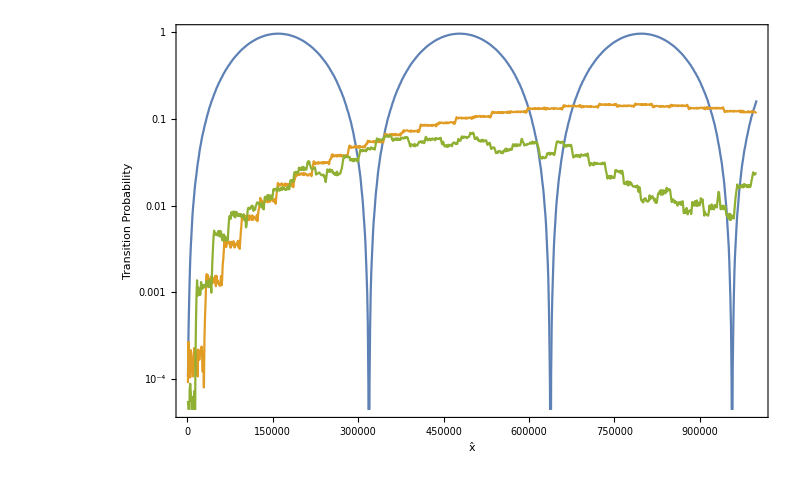

```mathematica
ListLogPlot[{
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[1]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[2]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit3[[1]]},{x,0,endpoint,Floor[endpoint/1000]}]
},Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks[1]}},GridLines->{gridlinesCode4[2], None},PlotRange->{(*{0,2.95*10^5}*)Automatic,Automatic}]
```

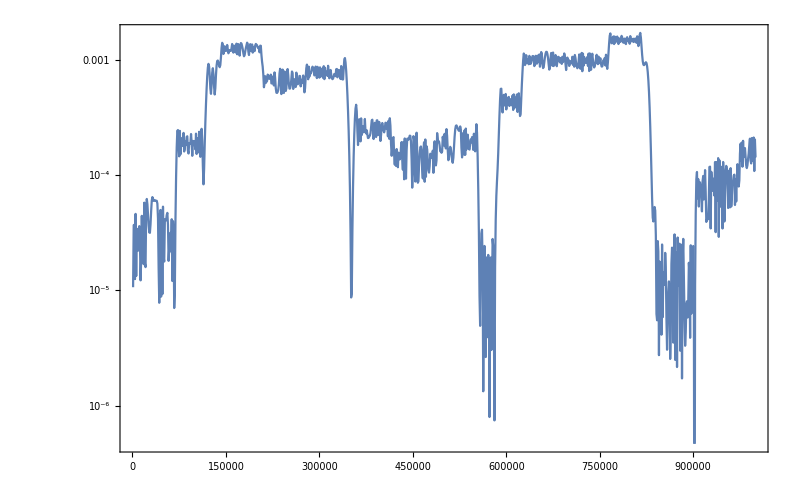

```mathematica
ListLogPlot[Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit3[[1]]},{x,0,endpoint,Floor[endpoint/1000]}] ,Joined->True,ImageSize->imgsize,Frame->True,GridLines->{gridlinesCode3[3], None}]
```

Q Values and wavelength

```mathematica
neuQValueListPaper1[[5,1]]
{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,1]]}
```

{3,-20}

{1,1/10}

```mathematica
neuQValueListPaper1=Part[qValueOrderdList[listNGenerator[2,20],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,1]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,1]]},{0,0},thetamV],1;;20];
Table[
{neuQValueListPaper1[[i,1]],neuQValueListPaper1[[i,2]],
widthNList[neuQValueListPaper1[[i,1]],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,1]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,1]]},{0,0},thetamV],
widthNList[neuQValueListPaper1[[i,1]],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,1]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,1]]},{0,0},thetamV]/(2 widthNList[{1,0},{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,1]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,1]]},{0,0},thetamV]neuQValueListPaper1[[i,2]]),
2Pi/(widthNList[neuQValueListPaper1[[i,1]],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,1]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,1]]},{0,0},thetamV]^2+(1-neuQValueListPaper1[[i,1]].{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,1]]})^2)^(1/2)},
{i,1,Length@neuQValueListPaper1}];
Grid@%
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

{-1,20} | 0. | 1.49282×10^-50 | ComplexInfinity | 4.20892×10^50
{0,10} | 0. | 5.014×10^-21 | ComplexInfinity | 1.25313×10^21
{1,0} | 0. | 0.0000193313 | ComplexInfinity | 325026.
{2,-10} | 0. | 5.32664×10^-30 | ComplexInfinity | 1.17958×10^30
{3,-20} | 0. | 5.28636×10^-60 | ComplexInfinity | 1.18857×10^60
{0,1} | 465.071 | 0.00193519 | 0.107625 | 6.9813
{0,-1} | 568.42 | 0.00193519 | 0.0880567 | 5.71198
{0,2} | 8965.27 | 0.0000892332 | 0.000257438 | 7.85398
{0,-2} | 13447.9 | 0.0000892332 | 0.000171625 | 5.23599
{1,1} | 101914. | 9.81218×10^-7 | 2.49023×10^-7 | 62.8319
{-1,0} | 103459. | 0.0000193313 | 4.83283×10^-6 | 3.14159
{1,-1} | 124562. | 8.02815×10^-7 | 1.66701×10^-7 | 62.8319
{0,3} | 340310. | 2.05695×10^-6 | 1.56335×10^-7 | 8.97598
{0,-3} | 632005. | 2.05695×10^-6 | 8.41805×10^-8 | 4.83322
{-1,-1} | 2.1402×10^6 | 9.81218×10^-7 | 1.18582×10^-8 | 2.99199
{-1,1} | 2.36667×10^6 | 8.02815×10^-7 | 8.77376×10^-9 | 3.30694
{1,2} | 8.10406×10^6 | 2.4679×10^-8 | 7.87651×10^-11 | 31.4159
{1,-2} | 1.21561×10^7 | 1.64527×10^-8 | 3.50067×10^-11 | 31.4159
{0,4} | 1.89825×10^7 | 3.1608×10^-8 | 4.30678×10^-11 | 10.472
{0,-4} | 4.42925×10^7 | 3.1608×10^-8 | 1.84576×10^-11 | 4.48799

```mathematica
neuQValueListPaper2=Part[qValueOrderdList[listNGenerator[2,100],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,2]]},{0,0},thetamV],1;;100];
neuGridListPaper2=Table[
{neuQValueListPaper2[[i,1]],neuQValueListPaper2[[i,2]],
widthNList[neuQValueListPaper2[[i,1]],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,2]]},{0,0},thetamV],
widthNList[neuQValueListPaper2[[i,1]],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,2]]},{0,0},thetamV]/(2 widthNList[{1,0},{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,2]]},{0,0},thetamV] neuQValueListPaper2[[i,2]]),
2Pi/(widthNList[neuQValueListPaper2[[i,1]],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,2]]},{0,0},thetamV]^2+(1-neuQValueListPaper2[[i,1]].{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]]})^2)^(1/2)
},
{i,1,Length@neuQValueListPaper2}];

PrependTo[neuGridListPaper2,{"{n} List","RD","Width","RD Shifted 1st","Oscillation Wavelength"}];
Grid@%
```

Power::infy: Infinite expression 1/0. encountered.

{n} List | RD | Width | RD Shifted 1st | Oscillation Wavelength
{1,0} | 0. | 1.53974×10^-6 | ComplexInfinity | 4.08067×10^6
{1,2} | 130.747 | 1.52968×10^-6 | 0.00379918 | 31415.
{1,-2} | 130.799 | 1.52906×10^-6 | 0.00379615 | 31415.
{1,1} | 209.094 | 4.78254×10^-7 | 0.000742742 | 62831.1
{1,-1} | 209.136 | 4.78158×10^-7 | 0.000742445 | 62831.1
{1,4} | 267.643 | 1.49453×10^-6 | 0.00181329 | 15707.9
{1,-4} | 267.858 | 1.49333×10^-6 | 0.00181039 | 15707.9
{1,6} | 422.045 | 1.42165×10^-6 | 0.00109384 | 10471.9
{1,-6} | 422.552 | 1.41994×10^-6 | 0.00109122 | 10471.9
{1,3} | 550.734 | 5.44727×10^-7 | 0.000321187 | 20943.9
{1,-3} | 551.065 | 5.444×10^-7 | 0.000320802 | 20943.9
{1,8} | 619.504 | 1.29136×10^-6 | 0.000676899 | 7853.97
{1,-8} | 620.496 | 1.28929×10^-6 | 0.000674736 | 7853.97
{1,5} | 741.244 | 6.74541×10^-7 | 0.000295507 | 12566.4
{1,-5} | 741.986 | 6.73867×10^-7 | 0.000294917 | 12566.4
{1,7} | 814.193 | 8.59747×10^-7 | 0.000342897 | 8975.97
{1,-7} | 815.334 | 8.58544×10^-7 | 0.000341939 | 8975.97
{1,9} | 830.209 | 1.08406×10^-6 | 0.000424022 | 6981.31
{1,-9} | 831.705 | 1.08211×10^-6 | 0.000422498 | 6981.31
{1,11} | 834.225 | 1.31859×10^-6 | 0.000513272 | 5711.98
{1,-11} | 836.062 | 1.31569×10^-6 | 0.000511019 | 5711.98
{1,13} | 856.308 | 1.51814×10^-6 | 0.00057571 | 4833.22
{1,-13} | 858.538 | 1.5142×10^-6 | 0.000572725 | 4833.22
{1,15} | 925.393 | 1.62093×10^-6 | 0.000568801 | 4188.79
{1,10} | 925.987 | 1.07993×10^-6 | 0.000378714 | 6283.18
{1,-10} | 927.841 | 1.07777×10^-6 | 0.000377202 | 6283.18
{1,-15} | 928.173 | 1.61608×10^-6 | 0.000565398 | 4188.79
{1,17} | 1093.06 | 1.55527×10^-6 | 0.000462047 | 3695.99
{1,-17} | 1096.78 | 1.54999×10^-6 | 0.000458916 | 3695.99
{1,22} | 1373.33 | 1.60195×10^-6 | 0.000378786 | 2855.99
{1,-22} | 1379.39 | 1.59491×10^-6 | 0.000375468 | 2855.99
{1,19} | 1511.17 | 1.2573×10^-6 | 0.000270177 | 3306.94
{1,-19} | 1516.92 | 1.25254×10^-6 | 0.000268131 | 3306.94
{1,24} | 1528.03 | 1.57065×10^-6 | 0.000333786 | 2617.99
{1,-24} | 1535.38 | 1.56313×10^-6 | 0.000330597 | 2617.99
{1,20} | 1559.79 | 1.28222×10^-6 | 0.000266943 | 3141.59
{1,-20} | 1566.04 | 1.2771×10^-6 | 0.000264816 | 3141.59
{1,12} | 1567.71 | 7.65445×10^-7 | 0.000158551 | 5235.99
{1,-12} | 1571.48 | 7.63611×10^-7 | 0.000157792 | 5235.99
{0,89} | 1779.66 | 0.000556904 | 0.101616 | 6.33961
{1,29} | 1779.93 | 1.62928×10^-6 | 0.000297245 | 2166.62
{1,-29} | 1790.28 | 1.61986×10^-6 | 0.000293817 | 2166.62
{1,27} | 1802.44 | 1.49797×10^-6 | 0.000269876 | 2327.11
{0,88} | 1805.02 | 0.000549134 | 0.098791 | 6.33897
{0,-89} | 1811.62 | 0.000556904 | 0.0998236 | 6.22776
{1,-27} | 1812.2 | 1.4899×10^-6 | 0.000266977 | 2327.11
{0,-88} | 1837.07 | 0.000549134 | 0.0970674 | 6.22837
{0,90} | 1884.95 | 0.000525744 | 0.0905726 | 6.34025
{0,-90} | 1919.18 | 0.000525744 | 0.0889568 | 6.22714
{0,87} | 2014.59 | 0.000492061 | 0.0793147 | 6.33833
{0,-87} | 2049.95 | 0.000492061 | 0.0779465 | 6.22899
{1,32} | 2062.77 | 1.55131×10^-6 | 0.000244213 | 1963.5
{1,-32} | 2076.02 | 1.54141×10^-6 | 0.000241107 | 1963.5
{0,91} | 2115.01 | 0.000468507 | 0.0719324 | 6.34089
{0,-91} | 2153.86 | 0.000468507 | 0.070635 | 6.22652
{1,34} | 2165.39 | 1.57015×10^-6 | 0.000235465 | 1848.
{1,-34} | 2180.17 | 1.55951×10^-6 | 0.000232284 | 1848.
{1,37} | 2192.45 | 1.68761×10^-6 | 0.000249956 | 1698.16
{1,-37} | 2208.73 | 1.67517×10^-6 | 0.000246284 | 1698.16
{1,18} | 2356.75 | 7.63762×10^-7 | 0.000105236 | 3490.66
{1,-18} | 2365.25 | 7.61018×10^-7 | 0.000104481 | 3490.66
{1,26} | 2378.86 | 1.09296×10^-6 | 0.000149196 | 2416.61
{1,-26} | 2391.26 | 1.08729×10^-6 | 0.000147653 | 2416.61
{1,40} | 2464.32 | 1.62316×10^-6 | 0.000213888 | 1570.8
{1,-40} | 2484.12 | 1.61023×10^-6 | 0.000210493 | 1570.8
{0,92} | 2491.54 | 0.000397665 | 0.0518287 | 6.34153
{0,81} | 2504.75 | 0.000396008 | 0.0513407 | 6.33449
{0,-92} | 2537.81 | 0.000397665 | 0.0508838 | 6.22591
{0,-81} | 2545.65 | 0.000396008 | 0.0505157 | 6.2327
{0,80} | 2597.27 | 0.000381939 | 0.0477527 | 6.33386
{0,86} | 2599.38 | 0.000381399 | 0.0476464 | 6.33769
{0,-80} | 2639.16 | 0.000381939 | 0.0469947 | 6.23332
{0,-86} | 2644.48 | 0.000381399 | 0.0468339 | 6.22961
{1,31} | 2811.2 | 1.10273×10^-6 | 0.000127379 | 2026.83
{1,43} | 2815.78 | 1.52711×10^-6 | 0.000176113 | 1461.21
{1,-31} | 2828.69 | 1.09591×10^-6 | 0.000125809 | 2026.83
{1,25} | 2836.91 | 8.8124×10^-7 | 0.000100872 | 2513.27
{1,-43} | 2840.1 | 1.51403×10^-6 | 0.00017311 | 1461.21
{1,-25} | 2851.13 | 8.76845×10^-7 | 0.0000998681 | 2513.27
{0,75} | 2891.62 | 0.000343234 | 0.0385452 | 6.33066
{0,-75} | 2935.32 | 0.000343234 | 0.0379713 | 6.23641
{1,45} | 2992.42 | 1.5038×10^-6 | 0.000163189 | 1396.26
{1,21} | 2995.06 | 7.01155×10^-7 | 0.0000760204 | 2991.99
{1,42} | 3000.61 | 1.39972×10^-6 | 0.000151479 | 1496.
{1,-21} | 3007.66 | 6.98216×10^-7 | 0.0000753845 | 2991.99
{1,-45} | 3019.47 | 1.49033×10^-6 | 0.000160277 | 1396.26
{1,-42} | 3025.92 | 1.38801×10^-6 | 0.000148955 | 1496.
{1,88} | 3032.72 | 2.90169×10^-6 | 0.000310699 | 713.998
{1,55} | 3045.38 | 1.80602×10^-6 | 0.000192576 | 1142.4
{1,89} | 3058.46 | 2.90997×10^-6 | 0.000308963 | 705.976
{0,93} | 3062.24 | 0.000323522 | 0.0343073 | 6.34217
{1,52} | 3071.79 | 1.69283×10^-6 | 0.000178955 | 1208.3
{1,-55} | 3079.06 | 1.78626×10^-6 | 0.000188385 | 1142.4
{1,46} | 3081.09 | 1.49298×10^-6 | 0.000157351 | 1365.91
{1,-88} | 3086.57 | 2.85106×10^-6 | 0.000299952 | 713.998
{1,35} | 3090.8 | 1.13239×10^-6 | 0.000118973 | 1795.2
{1,-52} | 3103.9 | 1.67531×10^-6 | 0.000175271 | 1208.3
{1,-46} | 3109.57 | 1.4793×10^-6 | 0.000154482 | 1365.91
{1,-35} | 3112.51 | 1.12449×10^-6 | 0.000117319 | 1795.2
{1,-89} | 3113.38 | 2.85863×10^-6 | 0.000298157 | 705.976

```mathematica
neuQValueListPaper3=Part[qValueOrderdList[listNGenerator[3,60],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]],kListKK3NumLimit[[3]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,2]],aListKK3NumLimit[[3]]},{0,0,0},thetamV],1;;15];
neuWidthListPaper3=Table[widthNList[neuQValueListPaper3[[i,1]],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]],kListKK3NumLimit[[3]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,2]],aListKK3NumLimit[[3]]},{0,0,0},thetamV],{i,1,Length@neuQValueListPaper3}];
neuGridListPaper3=Table[
{neuQValueListPaper3[[i,1]],
neuQValueListPaper3[[i,2]],
neuWidthListPaper3[[i]],
neuWidthListPaper3[[i]]/(2 neuWidthListPaper3[[1]] neuQValueListPaper3[[i,2]]),
2Pi/(neuWidthListPaper3[[i]]^2+(1-neuQValueListPaper3[[i,1]].{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]],kListKK3NumLimit[[3]]})^2)^(1/2)},
{i,1,Length@neuQValueListPaper3}];
PrependTo[neuGridListPaper3,{"{n} List","RD","Width","RD Shifted 1st","Oscillation Wavelength"}];
Grid@%
```

Power::infy: Infinite expression 1/0. encountered.

{n} List | RD | Width | RD Shifted 1st | Oscillation Wavelength
{1,0,0} | 0. | 2.2708×10^-7 | ComplexInfinity | 2.76694×10^7
{1,-35,11} | 8.95625 | 1.57292×10^-7 | 0.0386697 | 4.43258×10^6
{1,35,-11} | 8.95628 | 1.57292×10^-7 | 0.0386695 | 4.43258×10^6
{1,-19,6} | 60.4489 | 1.63102×10^-7 | 0.00594101 | 637197.
{1,19,-6} | 60.4501 | 1.63098×10^-7 | 0.00594077 | 637197.
{1,-54,17} | 65.8547 | 1.71105×10^-7 | 0.00572092 | 557546.
{1,54,-17} | 65.8562 | 1.71101×10^-7 | 0.00572066 | 557546.
{1,51,-16} | 114.9 | 6.12865×10^-8 | 0.00117445 | 892233.
{1,-51,16} | 114.902 | 6.12856×10^-8 | 0.00117442 | 892233.
{1,13,-4} | 120.309 | 2.2243×10^-7 | 0.00407085 | 234786.
{1,-13,4} | 120.316 | 2.22418×10^-7 | 0.00407041 | 234786.
{1,29,-9} | 147.648 | 2.38479×10^-7 | 0.00355642 | 178440.
{1,-29,9} | 147.659 | 2.38463×10^-7 | 0.00355592 | 178440.
{1,48,-15} | 157.795 | 1.60662×10^-7 | 0.00224187 | 247836.
{1,-48,15} | 157.803 | 1.60654×10^-7 | 0.00224164 | 247836.

### Two Frequencies

```mathematica
kListTwoFreq={1,,1/10};
aListTwoFreq={0.0001,0.1};
(*aListKK3NumLimit={0.0001,{a2FromQ[0.0001,1],a2FromQ[0.0001,1]},a2FromQ[0.0001,1]};*)
```

### Rabi Oscillations

```mathematica
a2FromQ[0.0001,1]
```

0.0141421

```mathematica
kListRabi={1,{1/(10),1/(3000)},1/(300Pi)};
aListRabi={0.0001,{0.05,0.05},0.05};
(*aListRabi={0.0001,{10a2FromQ[0.0001,1],10a2FromQ[0.0001,1]},10a2FromQ[0.0001,1]};*)
```

```mathematica
solNumRabi[kList_,aList_,endpointModule_]:=Module[{sysM,lenM},

lenM=Length@kList;

(*sysM=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(Total[Table[aList[[n]]Cos[kList[[n]]x],{n,1,lenM}]])PauliMatrix[1]/2(*+(Total[Table[aList[[n]]Sin[kList[[n]]x],{n,1,lenM}]])PauliMatrix[2]/2*)).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};
*)
sysM=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(Total[Table[aList[[n]]Cos[kList[[n]]x],{n,1,lenM}]])PauliMatrix[1]/2(*+(aList[[1]]Sin[kList[[1]]x])PauliMatrix[2]/2*)(*+(Total[Table[aList[[n]]Sin[kList[[n]]x],{n,1,lenM}]])PauliMatrix[2]/2*)).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

NDSolve[sysM,{psi1,psi2},{x,0,endpointModule}]
]
```

```mathematica
solNumRabi0=solNumRabi[{kListRabi[[1]]},{aListRabi[[1]]},endpoint]
```

{{psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

```mathematica
solNumRabi1=solNumRabi[{kListRabi[[1]],kListRabi[[2,1]]},{aListRabi[[1]],aListRabi[[2,1]]},endpoint]
```

{{psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

```mathematica
solNumRabi2=solNumRabi[{kListRabi[[1]],kListRabi[[2,2]]},{aListRabi[[1]],aListRabi[[2,2]]},endpoint]
```

{{psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

```mathematica
solNumRabi3=solNumRabi[{kListRabi[[1]],kListRabi[[2,2]],kListRabi[[3]]},{aListRabi[[1]],aListRabi[[2,2]],aListRabi[[3]]},endpoint]
```

{{psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

```mathematica
solNumRabi1
```

{{psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

```mathematica
solNumRabiList0=Table[{x,(Abs[psi2[x]]^2)/.solNumRabi0[[1]]},{x,0,endpoint/5,Floor[endpoint/10000]}];
solNumRabiList1=Table[{x,(Abs[psi2[x]]^2)/.solNumRabi1[[1]]},{x,0,endpoint/5,Floor[endpoint/10000]}];
solNumRabiList2=Table[{x,(Abs[psi2[x]]^2)/.solNumRabi2[[1]]},{x,0,endpoint/5,Floor[endpoint/10000]}];
solNumRabiList3=Table[{x,(Abs[psi2[x]]^2)/.solNumRabi3[[1]]},{x,0,endpoint/5,Floor[endpoint/10000]}];
```

```mathematica
interferenceRabiPyGridLines=gridlinesCodeRabi[i_]:=Table[{n,Directive[plotstylecolorList[[i]],Dashed]},{n,0,endpoint,(Pi)/kListRabi[[2,i]]}]
gridlinesCodeRabiZeros[i_]:=Table[{n-(Pi/2)/kListRabi[[2,i]],Directive[plotstylecolorList[[i]],Dashed]},{n,0,endpoint,(Pi)/kListRabi[[2,i]]}]
```

```mathematica
interferenceRabiPyGridLines=Table[N@n,{n,0,endpoint,(Pi)/kListRabi[[2,2]]}];
interferenceRabiPyGridLinesZeros=Table[N[n-(Pi/2)/kListRabi[[2,2]]],{n,0,endpoint,(Pi)/kListRabi[[2,2]]}];
```

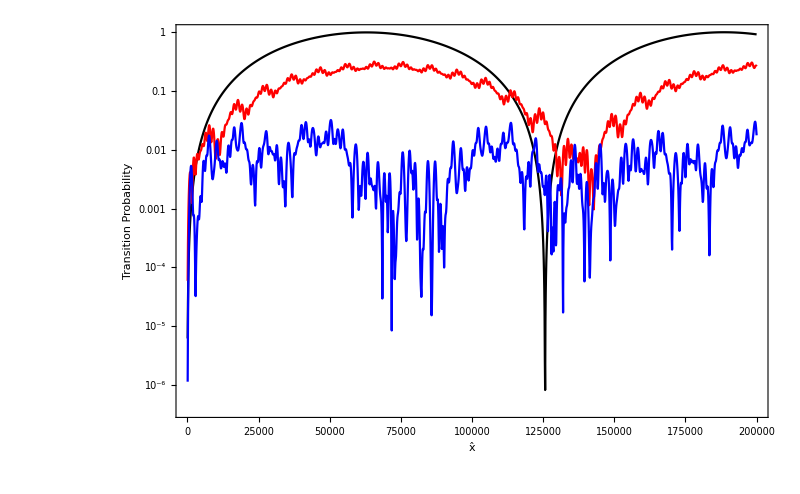

```mathematica
ListLogPlot[{
solNumRabiList0,
(*solNumRabiList1,*)
solNumRabiList2,
solNumRabiList3
}
,Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks[1]}},GridLines->{gridlinesCodeRabiZeros[2], None},PlotRange->{(*{0,2 10^5}*)Automatic,Automatic},PlotStyle->{Black,Red,Blue,Magenta}]
```

```mathematica
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/rabi-interference1-three-modes-k1-1-a1-"<>ToString[N@aListRabi[[1]]]<>".csv",solNumRabiList0]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/rabi-interference1-three-modes-k1-1-k2-"<>"1o10"<>"-a1-"<>ToString[N@aListRabi[[1]]]<>"-a2-"<>ToString[N@aListRabi[[2,1]]]<>".csv",solNumRabiList1]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/rabi-interference2-three-modes-k1-1-k2-"<>"1o3000"<>"-a1-"<>ToString[aListRabi[[1]]]<>"-a2-"<>ToString[aListRabi[[2,2]]]<>".csv",solNumRabiList2]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/rabi-interference3-three-modes-k1-1-k2-1o3000-k3-1o3000Pi-a1-"<>ToString[aListRabi[[1]]]<>"-a2-"<>ToString[aListRabi[[2,2]]]<>"-a3-"<>ToString[aListRabi[[3]]]<>".csv",solNumRabiList3]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/rabi-interference-three-modes-interferencePyGridLines.csv",interferenceRabiPyGridLines]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/rabi-interference-three-modes-interferencePyGridLinesZeros.csv",interferenceRabiPyGridLinesZeros]
```

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/rabi-interference1-three-modes-k1-1-a1-0.0001.csv

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/rabi-interference1-three-modes-k1-1-k2-1o10-a1-0.0001-a2-0.05.csv

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/rabi-interference2-three-modes-k1-1-k2-1o3000-a1-0.0001-a2-0.05.csv

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/rabi-interference3-three-modes-k1-1-k2-1o3000-k3-1o3000Pi-a1-0.0001-a2-0.05-a3-0.05.csv

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/rabi-interference-three-modes-interferencePyGridLines.csv

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/rabi-interference-three-modes-interferencePyGridLinesZeros.csv

### Calculate Widths, Q values, and more

```mathematica
Part[qValueOrderdList[listNGenerator[2,20],{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,3]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,3]]},twophiListKK,thetamV],1;;10]
Grid@%
```

{{{1,0},0.},{{0,18},155.733},{{0,19},167.275},{{0,-18},174.664},{{0,17},180.519},{{0,-19},188.811},{{0,-17},201.173},{{0,20},209.025},{{0,-20},237.448},{{0,13},271.102}}

{1,0} | 0.
{0,18} | 155.733
{0,19} | 167.275
{0,-18} | 174.664
{0,17} | 180.519
{0,-19} | 188.811
{0,-17} | 201.173
{0,20} | 209.025
{0,-20} | 237.448
{0,13} | 271.102

```mathematica
twoaListKK3NumLimit[[2,3]]/twokListKK3NumLimit[[2,3]]Cos[2thetamV]
```

20.0495

```mathematica
10000widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]
```

0.0692269

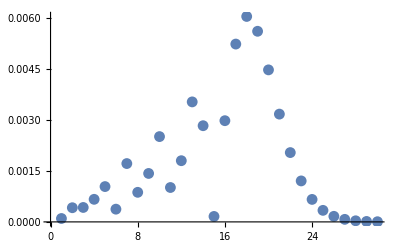

```mathematica
ListPlot[Table[widthNList[{0,n},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,3]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,3]]},twophiListKK,thetamV],{n,1,30}],GridLines->{None,{10000widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]}}]
```

```mathematica
widthList10000={widthNList[{1,0},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,3]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,3]]},twophiListKK,thetamV],
widthNList[{0,1},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,3]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,3]]},twophiListKK,thetamV],
widthNList[{0,2},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,3]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,3]]},twophiListKK,thetamV]}
```

{1.13196×10^-6,0.000100129,0.000417517}

```mathematica
Part[qValueOrderdList[listNGenerator[2,10],{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,2]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,2]]},twophiListKK,thetamV],1;;10]
Grid@%
```

{{{1,0},0.},{{1,1},4595.2},{{1,-1},4624.55},{{0,1},7470.33},{{0,-1},7518.04},{{0,2},74156.3},{{0,-2},75106.5},{{1,2},182468.},{{1,-2},184806.},{{-1,0},291830.}}

{1,0} | 0.
{1,1} | 4595.2
{1,-1} | 4624.55
{0,1} | 7470.33
{0,-1} | 7518.04
{0,2} | 74156.3
{0,-2} | 75106.5
{1,2} | 182468.
{1,-2} | 184806.
{-1,0} | 291830.

```mathematica
widthList100={widthNList[{1,0},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,2]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,2]]},twophiListKK,thetamV],
widthNList[{0,1},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,2]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,2]]},twophiListKK,thetamV],
widthNList[{0,2},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,2]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,2]]},twophiListKK,thetamV]}
```

{6.85329×10^-6,0.000133437,0.0000133992}

```mathematica
Part[qValueOrderdList[listNGenerator[2,10],{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,1]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,1]]},twophiListKK,thetamV],1;;10]
Grid@%
```

{{{1,0},0.},{{1,1},795.19},{{1,-1},800.268},{{0,2},1049.25},{{0,-2},1062.7},{{0,1},1292.72},{{0,-1},1300.98},{{0,3},1902.27},{{0,-3},1938.95},{{1,2},2581.77}}

{1,0} | 0.
{1,1} | 795.19
{1,-1} | 800.268
{0,2} | 1049.25
{0,-2} | 1062.7
{0,1} | 1292.72
{0,-1} | 1300.98
{0,3} | 1902.27
{0,-3} | 1938.95
{1,2} | 2581.77

```mathematica
widthList1000={widthNList[{1,0},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,1]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,1]]},twophiListKK,thetamV],
widthNList[{0,1},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,1]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,1]]},twophiListKK,thetamV],
widthNList[{0,2},{twokListKK3NumLimit[[1]],twokListKK3NumLimit[[2,1]]},{twoaListKK3NumLimit[[1]],twoaListKK3NumLimit[[2,1]]},twophiListKK,thetamV]}
```

{1.53015×10^-6,0.000771098,0.000946993}

```mathematica
Grid@{widthList100,widthList1000,widthList10000}
```

6.85329×10^-6 | 0.000133437 | 0.0000133992
1.53015×10^-6 | 0.000771098 | 0.000946993
1.13196×10^-6 | 0.000100129 | 0.000417517

```mathematica
ListLogPlot[{Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[1]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[2]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[1,1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[2,1]]},{x,0,endpoint,Floor[endpoint/1000]}]
},Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks[1]}},
PlotStyle->Join[Take[plotstylecolorList,3],{Directive[plotstylecolorList[[2]],Dashed],Directive[plotstylecolorList[[3]],Dashed],Directive[plotstylecolorList[[3]],Dashed]}],PlotLabel->"Resonance Destruction (A_2=10000B_1)",PlotLegends->Placed[{"k_2=k_1/10","k_2=k_1/1000","k_2=k_1/10000","k_2=k_1/20000","{1,0} Mode with k_2=k_1/1000","{1,0} Mode with k_2=k_1/10000","{1,0} Mode with k_2=k_1/20000"},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},PlotRange->{Automatic,{10^(-9),10}},GridLines->{gridlinesCode4[2], None},GridLinesStyle->Directive[Orange,Dashed]]
```

-Graphics-

```mathematica
(*ListLogPlot[{Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[1]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[2]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[3]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solNumStashLimit[[4]][[1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[2,1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[3,1]]},{x,0,endpoint,Floor[endpoint/1000]}],
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.twokListKK3NumLimit10Mode[[4,1]]},{x,0,endpoint,Floor[endpoint/1000]}]
},Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks[1]}},
PlotStyle->Join[Take[plotstylecolorList,4],{Directive[plotstylecolorList[[2]],Dashed],Directive[plotstylecolorList[[3]],Dashed],Directive[plotstylecolorList[[4]],Dashed]}],PlotLabel->"Resonance Destruction (A_2=10000B_1)",PlotLegends->Placed[{"k_2=k_1/10","k_2=k_1/1000","k_2=k_1/10000","k_2=k_1/20000","{1,0} Mode with k_2=k_1/1000","{1,0} Mode with k_2=k_1/10000","{1,0} Mode with k_2=k_1/20000"},{Center,Above}],LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},PlotRange->{Automatic,{10^(-9),10}},GridLines->{gridlinesCode4[4], None},GridLinesStyle->Directive[Orange,Dashed]]*)
```

Finally some figures about the actual matter profile

```mathematica
matterProfiles
```

{0.0000357347 Sin[0.0000357347 x],0.0000346135 Sin[x/10],0.0000692269 Sin[x/10],0.00010384 Sin[x/10],0.000346135 Sin[x/10],0.00346135 Sin[x/10],0.0346135 Sin[x/10]}

```mathematica
omegaMKK
```

3.67552×10^-17

```mathematica
matterProfilesTicks:=Table[{x,ScientificForm[MeVInverse2km[x/omegaMKK],2]},{x,0,Pi/twokListKK3Num[[1]],Pi/twokListKK3Num[[1]]/5}];

matterProfiles=Join[{twoaListKK3Num[[1]]*Sin[twokListKK3Num[[1]]x]},twoaListKK3Num[[2]]*Sin[twokListKK3Num[[2]]x]];
(*Plot[matterProfiles,{x,0,endpoint/10000},ImageSize->imgsize,PlotLegends->Placed[twoaListKK3Num[[2]],{Center,Above}],Frame->True,PlotRange->{{0,Pi/twokListKK3Num[[2,1]]},{10^(-6),0.1}},GridLines->{None, twoaListKK3Num[[2]]}]
*)
LogPlot[matterProfiles,{x,0,endpoint/10000},ImageSize->imgsize,PlotLegends->Placed[
Join[{twoaListKK3Num[[1]]},twoaListKK3Num[[2]]],{Center,Above}],Frame->True,PlotRange->{{0,Pi/twokListKK3Num[[1]]},{10^(-6),1}},PlotLabel->"Matter Profiles within Half Wavelength",PlotStyle->Join[{Black},plotstylecolorList],FrameLabel->{{"Matter Density (ω_m)",None},{"x̂","Distance (km)"}},FrameTicks->{{Automatic,Automatic},{Automatic,matterProfilesTicks}},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15}]
```

Some test of plotting

```mathematica
plotfrac[fractionk2Input_,fractionA2Input_,title_,legendsplotfrac_,color_]:=Module[{fractionk2M,fractionA2M},

fractionk2M=fractionk2Input;
fractionA2M=fractionA2Input;

twokListKK3={onekListKK[[1]],onekListKK[[1]]*fractionk2M};
twoaListKK3={oneaListKK[[1]],widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV]*fractionA2M};
lambdaNKK3=0.5*Cos[2thetaV]omegaVKK +twoaListKK3[[2]]*omegaMKK(*MeV*);
omegaMKK3=OmegaMatter2[lambdaNKK3,thetaV,omegaVKK](*MeV*);
thetamV3=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaNKK3/omegaVKK)^2)]/2,Pi];
onekListKK3=oneaListKK[[1]]*omegaMKK/omegaMKK3;
oneaListKK3=(*{0.1};*)oneaListKK[[1]]*omegaMKK/omegaMKK3;


(*Part[qValueOrderdList[listNGenerator[1,10],onekListKK3,oneaListKK3,onephiListKK,thetamV3],1;;10];
Grid@%;
*)
(*widthNList[{1},onekListKK,oneaListKK,onephiListKK,thetamV];
widthNList[{1},onekListKK2,oneaListKK2,onephiListKK,thetamV2];
*)


Legended[Show[Table[pltNList[{{1}},{onekListKK3[[i]]},{oneaListKK3[[i]]},onephiListKK,thetamV3[[i]],endpoint,legendsplotfrac[[i]],color[[i]],None,None],{i,1,Length@oneaListKK3}],ImagePadding->{{Automatic, Automatic}, {Automatic, 20}},PlotLabel->title]
,Placed[LineLegend[color,legendsplotfrac],{Center,Above}]]

]
```

```mathematica
plotfrac[{1/10,1/10,1/10},{10,20,30},"Resonance Destruction (k2=k1/10)",{"A2=B1*10,A2=B1*20,A2=B1*30"},{Red,Blue,Orange}]
```

```mathematica
?pltNList
```

plot the result of solNList; Parameters taken are [listInput_,kNList_,aNList_,phiNList_,thetam_,endpoint_,legends_,color_,frameTicks_,frameLabel_,startpoint_:0]

```mathematica
(*pltNList[{{1}},onekListKK,oneaListKK,onephiListKK,thetamV,endpoint,"Mode n=1 with One Perturbation Only",Black,None,None];*)
solRes=solNList[{{1}},onekListKK,oneaListKK,onephiListKK,thetamV,endpoint];
```

```mathematica
solResList=Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solRes[[1]]},{x,0,endpoint,Floor[endpoint/1000]}];
```

```mathematica
solResList
```

## Calculate the Q Values

```mathematica
kListKK3NumLimit
aListKK3NumLimit
```

{1,{1/π,1/(1000 π)},1/(543 π)}

{0.0001,{0.0141421,0.0141421},0.0141421}

```mathematica
?qValue
```

calcualte the ratio of the EFFECTIVE distance and Effective Width (bCoefN)

```mathematica
Table[qValue[{i},{k1},{a1},{0},thetam],{i,1,3}]
```

{0.,1.11987×10^9,9.71798×10^13}

```mathematica
?qValueOrderdList
```

gives ordered list of qValues and also their corresponding integer combinations; Example, qValueOrderdList[listNGenerator[6,3],kNListTest,aNListTest,phiNListTest,thetamTest]

```mathematica
?listNGenerator
```

generate a list of numbers; Example, listNGeneratorTest2[6,3] gives us {{-3,3},{-3,3},{-3,3},{-3,3},{-3,3},{-3,3}}

```mathematica
?listNGeneratorFormat2
```

generate a complete list given the upper limits; As an example listNGeneratorFormat2[{3,3,3}] gives us{{-3,-2,-1,0,1,2,3},{-3,-2,-1,0,1,2,3},{-3,-2,-1,0,1,2,3}}

```mathematica
listNGenerator[2,4]
```

{{-4,4},{-4,4}}

```mathematica
a2PureRabi
```

{0.000447214,0.0244949}

```mathematica
{k1,k2P}
{a1,a2PureRabi}
```

{1,0.01}

```mathematica
thetam
```

0.198931

```mathematica
{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,1]]}
{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]],kListKK3NumLimit[[3]]}
```

{1,1/π}

{1,1/(1000 π),1/(543 π)}

```mathematica
qvaluelist1=qValueOrderdList[listNGenerator[2,60],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,1]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,1]]},{0,0},thetamV];
qvaluelist2=qValueOrderdList[listNGenerator[2,100],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,2]]},{0,0},thetamV];
```

```mathematica
qvaluelist3=qValueOrderdList[listNGenerator[3,100],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]],kListKK3NumLimit[[3]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,2]],aListKK3NumLimit[[3]]},{0,0,0},thetamV];
```

```mathematica
(*Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/interference3-three-modes-k1-1-k2-1o1000Pi-k3-1o543-a1-"<>ToString[aListKK3NumLimit[[1]]]<>"-a2-"<>ToString[aListKK3NumLimit[[2,2]]]<>"-a3-"<>ToString[aListKK3NumLimit[[3]]]<>"qvalues-data-list-each-modes.csv",qvaluelist3[[1;;100000]]]*)
```

```mathematica
Timing[qValueOrderdList[listNGenerator[3,10],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]],kListKK3NumLimit[[3]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,2]],aListKK3NumLimit[[3]]},{0,0,0},thetamV]][[1]]*1000
```

1295.37

```mathematica
{
{{1,2},{2,3}}//Grid,
{{1,2},{2,3}}//Grid
}
```

{1 | 2
2 | 3,1 | 2
2 | 3}

```mathematica
{
qvaluelist1[[1;;10]]//Grid,
qvaluelist2[[1;;10]]//Grid,
qvaluelist3[[1;;10]]//Grid
}
```

{{1,0} | 0.
{0,1} | 248.873
{0,-1} | 481.292
{0,2} | 6477.51
{0,-2} | 29173.9
{0,3} | 78458.1
{-1,0} | 103283.
{1,1} | 608730.
{1,-1} | 1.17721×10^6
{0,-3} | 3.40313×10^6,{1,0} | 0.
{1,1} | 215.309
{1,-1} | 215.446
{1,2} | 323.895
{1,-2} | 324.307
{1,4} | 590.72
{1,-4} | 592.226
{1,3} | 741.798
{1,-3} | 743.216
{1,6} | 806.351,{1,0,0} | 0.
{1,35,-19} | 17.913
{1,-35,19} | 17.9131
{1,-11,6} | 53.225
{1,11,-6} | 53.2267
{1,37,-20} | 63.8707
{1,-37,20} | 63.8775
{1,-22,12} | 111.436
{1,22,-12} | 111.443
{1,39,-21} | 129.027}

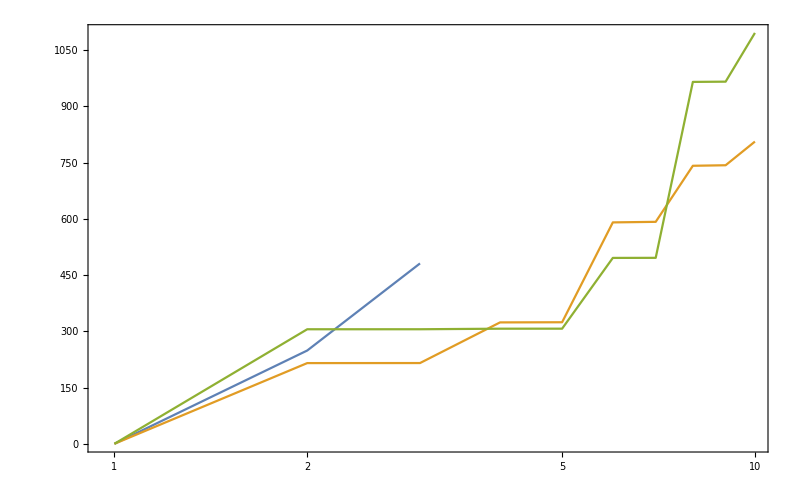

```mathematica
ListLogLinearPlot[{qvaluelist1[[1;;3,2]],
qvaluelist2[[1;;10,2]],
qvaluelist3[[1;;10,2]]},Joined->True,Frame->True,ImageSize->imgsize]
```

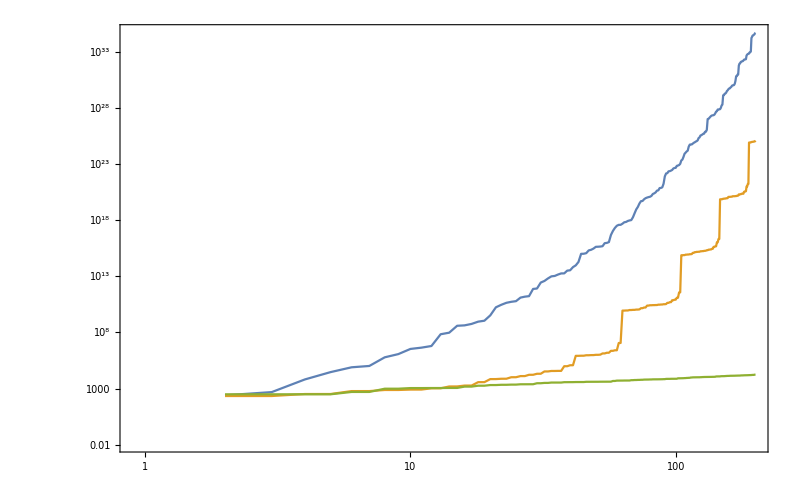

```mathematica
ListLogLogPlot[{qvaluelist1[[1;;200,2]],
qvaluelist2[[1;;200,2]],
qvaluelist3[[1;;200,2]]},Joined->True,Frame->True,ImageSize->imgsize]
```

Calculate the wavelength

```mathematica
qvaluelist1[[1,1]]
```

{1,0}

```mathematica
endN=100
```

100

```mathematica
widthlist1=Table[widthNList[qvaluelist1[[1;;endN,1]][[i]],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,1]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,1]]},{0,0},thetamV],{i,1,endN}];
widthlist2=Table[widthNList[qvaluelist2[[1;;endN,1]][[i]],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,2]]},{0,0},thetamV],{i,1,endN}];
widthlist3=Table[widthNList[qvaluelist3[[1;;endN,1]][[i]],{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]],kListKK3NumLimit[[3]]},{aListKK3NumLimit[[1]],aListKK3NumLimit[[2,2]],aListKK3NumLimit[[3]]},{0,0,0},thetamV],{i,1,endN}];
```

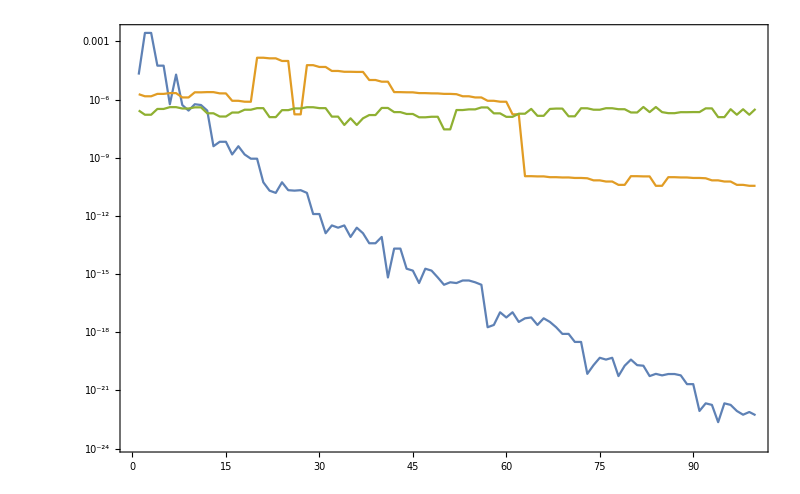

```mathematica
ListLogPlot[{widthlist1,widthlist2,widthlist3},Joined->True,Frame->True,ImageSize->imgsize,PlotRange->Full]
```

```mathematica
{wavelengthlist1=2Pi/(widthlist1*√(1+qvaluelist1[[1;;endN,2]]^2)),
wavelengthlist2=2Pi/(widthlist2*√(1+qvaluelist2[[1;;endN,2]]^2)),
wavelengthlist3=2Pi/(widthlist3*√(1+qvaluelist3[[1;;endN,2]]^2))}//Grid
```

{{324472.,9.217,4.76608,17.2909,3.83912,139.408,3.14159,19.7392,19.7392,3.21402,2.71024,3.73623,22.9952,9.8696,2.38305,9.8696,2.76398,4.60853,6.28319,2.0944,6.57974,10.6216,9.21707,2.12634,4.76609,2.42449,1.89349,2.34299,6.57974,6.01221,17.2909,4.9348,3.83912,1.91956,6.90567,1.72775,2.65856,8.64547,4.9348,2.15927,139.408,3.14159,1.5708,3.21402,3.94784,15.383,1.5887,1.74944,3.07236,5.1159,3.73623,3.94784,2.71024,1.45501,1.7066,1.94636,69.7042,22.9952,2.76398,3.28987,1.47036,4.60853,2.38305,1.60701,3.63871,1.35512,1.86812,3.28987,4.0629,1.77167,2.0944,1.25664,27.5374,6.01221,2.42449,2.12634,1.36842,10.6216,2.81989,1.26807,2.0634,1.48603,4.46106,2.81989,2.34299,1.89349,1.18143,1.34208,3.36938,1.62575,8.64547,1.91956,2.15927,11.4976,1.19152,1.27971,2.30427,2.65856,1.72775,2.4674},{3.32075×10^6,19739.,19739.,9869.56,9869.56,4934.8,4934.8,6579.73,6579.73,3289.87,3289.87,2625.61,2593.73,2979.18,2944.88,6913.53,6900.34,7188.49,7169.45,37.8622,37.4746,33.467,32.6047,43.636,42.756,23788.,23742.6,63.2496,62.7658,77.3893,76.9901,122.981,121.894,127.114,126.169,128.059,127.142,331.251,322.511,385.55,382.859,1224.58,1206.78,1201.44,1194.57,1275.41,1264.09,1286.79,1275.37,1267.32,1256.08,1292.9,1637.64,1633.77,1863.6,1864.54,2744.84,2743.95,3039.4,3033.69,13460.7,13222.3,2.0089×10^7,1.89906×10^7,1.92133×10^7,1.84213×10^7,2.01778×10^7,1.97961×10^7,2.04568×10^7,2.03572×10^7,2.13846×10^7,2.09634×10^7,2.1496×10^7,2.73131×10^7,2.71947×10^7,3.1248×10^7,3.09806×10^7,4.58702×10^7,4.53204×10^7,1.55915×10^7,1.53845×10^7,1.55993×10^7,1.55398×10^7,4.72059×10^7,4.65049×10^7,1.6465×10^7,1.62567×10^7,1.66338×10^7,1.65487×10^7,1.7358×10^7,1.73183×10^7,1.79381×10^7,2.28095×10^7,2.25007×10^7,2.56586×10^7,2.54967×10^7,3.73428×10^7,3.72473×10^7,4.11807×10^7,3.95496×10^7},{2.29097×10^7,2.1229×10^6,2.1231×10^6,359495.,359556.,241920.,241992.,162934.,163032.,122734.,122815.,223440.,223516.,310574.,310646.,171595.,171698.,96902.9,96983.6,68191.7,68263.1,166598.,166633.,72167.6,72252.3,58494.3,58580.6,43198.1,43268.7,47208.5,47301.8,119070.,119081.,280523.,127055.,260079.,117859.,79678.3,79739.6,32793.5,32876.2,52188.5,52258.6,60509.9,60583.2,89406.3,89466.6,79300.3,79315.9,349371.,349228.,34017.7,34081.4,28488.,28530.3,20822.3,20869.2,41657.9,41677.1,62172.7,62210.3,39388.1,39412.9,20659.2,46922.6,46483.2,20503.,19635.8,19707.7,47445.6,47488.7,17738.5,17810.6,19626.1,19679.4,15997.3,16055.3,17804.,17868.,25715.5,25783.1,13400.6,24582.9,13259.9,24237.9,27258.8,27305.5,23029.7,23062.2,22367.2,22417.3,13557.7,13599.5,38298.4,38343.5,14692.,28290.,14649.7,28115.2,14013.7}}

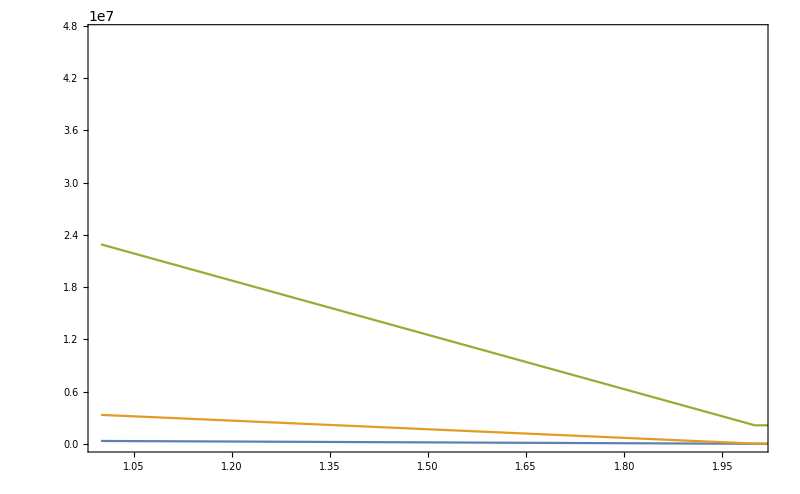

```mathematica
ListPlot[{wavelengthlist1=2Pi/(widthlist1*√(1+qvaluelist1[[1;;endN,2]]^2)),
wavelengthlist2=2Pi/(widthlist2*√(1+qvaluelist2[[1;;endN,2]]^2)),
wavelengthlist3=2Pi/(widthlist3*√(1+qvaluelist3[[1;;endN,2]]^2))},
Joined->True,Frame->True,ImageSize->imgsize,PlotRange->{{1,2},Full}]
```

Calculate the √(2(kn-k1)A1) and compare it with other’s

```mathematica
{1,3,2}/{1,2,3}
```

{1,3/2,2/3}

```mathematica
Table[qvaluelist1[[1;;endN,1]][[i]].{k1,k2P},{i,1,endN}]widthlist1[[1]]/widthlist1
```

{1.,0.0000706958,-0.0000706958,0.00690365,-0.00690365,1.01128,-1.,37.4023,70.8994,-1.01128,-37.4023,-70.8994,197.518,2971.2,-2971.2,12857.1,-197.518,-12857.1,43389.1,-43389.1,367940.,48223.2,2.50658×10^6,-367940.,1.83654×10^6,-48223.2,-1.83654×10^6,-2.50658×10^6,1.50298×10^7,-1.50298×10^7,3.00406×10^8,6.24016×10^7,1.58476×10^8,-6.24016×10^7,1.41283×10^7,-1.58476×10^8,-3.00406×10^8,-4.7922×10^8,4.7922×10^8,-1.41283×10^7,5.71179×10^10,2.82392×10^9,-2.82392×10^9,2.08161×10^10,1.34923×10^10,-5.34798×10^10,-2.08161×10^10,-1.34923×10^10,-5.71179×10^10,4.82913×10^9,1.53712×10^11,5.34798×10^10,1.25054×10^11,-1.25054×10^11,-1.53712×10^11,-4.82913×10^9,-1.00796×10^13,1.59607×10^13,3.68842×10^12,3.55405×10^12,-3.68842×10^12,1.69752×10^13,1.118×10^13,-3.55405×10^12,-1.59607×10^13,-1.118×10^13,-1.69752×10^13,1.00796×10^13,1.88644×10^12,-1.88644×10^12,2.45054×10^14,-2.45054×10^14,-2.52519×10^15,2.86399×10^15,8.24725×10^14,1.51087×10^15,-8.24725×10^14,6.89815×10^15,1.10534×10^15,-1.51087×10^15,-2.86399×10^15,-1.10534×10^15,-6.89815×10^15,2.52519×10^15,1.29653×10^16,1.11093×10^16,-1.11093×10^16,-1.29653×10^16,8.29026×10^14,-8.29026×10^14,6.60266×10^17,2.74016×10^17,2.23036×10^17,-7.74972×10^17,-2.74016×10^17,-2.23036×10^17,-6.60266×10^17,1.38245×10^18,1.0129×10^18,3.96706×10^17}

```mathematica
√(2Abs@Table[qvaluelist1[[1;;endN,1]][[i]].{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,1]]}-1,{i,1,endN}]widthlist1[[1]])/widthlist1
√(2Abs@Table[qvaluelist2[[1;;endN,1]][[i]].{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]]}-1,{i,1,endN}]widthlist2[[1]])/widthlist2
√(2Abs@Table[qvaluelist3[[1;;endN,1]][[i]].{kListKK3NumLimit[[1]],kListKK3NumLimit[[2,2]],kListKK3NumLimit[[3]]}-1,{i,1,endN}]widthlist3[[1]])/widthlist3
```

{0.,1.87586,2.60865,66.8719,141.918,2299.9,454.495,6714.53,12985.1,15147.1,18120.8,29846.6,829531.,746940.,1.52009×10^6,3.36412×10^6,2.39267×10^6,4.92312×10^6,6.97211×10^6,1.2076×10^7,1.12186×10^8,2.38394×10^8,3.34223×10^8,1.97346×10^8,3.37152×10^8,4.98976×10^8,5.34904×10^8,6.62898×10^8,4.86609×10^9,5.09057×10^9,2.93926×10^10,2.17586×10^10,3.22552×10^10,3.48871×10^10,7.21836×10^10,4.80812×10^10,7.49589×10^10,1.36764×10^11,1.81023×10^11,1.29088×10^11,1.97818×10^12,4.27818×10^11,6.05027×10^11,4.60769×10^12,5.2098×10^12,1.15624×10^13,6.55371×10^12,7.82622×10^12,1.33252×10^13,2.45705×10^13,2.14252×10^13,2.28239×10^13,2.03296×10^13,2.7746×10^13,3.17012×10^13,3.98348×10^13,1.03464×10^15,1.36799×10^15,8.76085×10^14,1.48913×10^15,1.20116×10^15,2.13757×10^15,1.93184×10^15,2.13065×10^15,3.43895×10^15,2.56182×10^15,3.35737×10^15,4.76244×10^15,9.42406×10^15,1.42713×10^16,3.41018×10^16,4.40252×10^16,4.16825×10^17,3.16812×10^17,2.08137×10^17,2.75468×10^17,2.77044×10^17,8.74394×10^17,4.95566×10^17,3.56711×10^17,5.40788×10^17,6.82658×10^17,1.34922×10^18,1.30256×10^18,1.71012×10^18,1.62187×10^18,2.05326×10^18,2.25956×10^18,4.04254×10^18,5.81972×10^18,6.11134×10^19,5.24089×10^19,5.93551×10^19,2.00124×10^20,6.65204×10^19,7.71004×10^19,1.18376×10^20,1.71612×10^20,1.5442×10^20,1.88377×10^20}

{0.,23.4759,23.4909,24.9718,25.0037,32.2043,32.2864,46.6968,46.786,35.893,36.0304,40.4085,40.6148,52.5171,52.8525,89.5102,89.7956,134.216,134.987,13.5009,13.544,14.5132,14.5502,19.8414,19.8793,529.515,531.88,32.6944,32.7361,40.4048,40.5208,65.0335,65.137,71.6833,71.729,72.9771,73.0468,190.575,190.636,232.321,232.839,1133.17,1137.5,1162.07,1165.4,1276.77,1279.21,1317.46,1323.76,1399.89,1401.23,1453.98,1861.,1861.89,2137.57,2140.63,3174.32,3181.9,3548.81,3564.09,15873.1,15926.2,1.74163×10^7,1.74163×10^7,1.78521×10^7,1.78521×10^7,1.96047×10^7,1.96047×10^7,2.02584×10^7,2.02584×10^7,2.14851×10^7,2.14851×10^7,2.23046×10^7,2.85553×10^7,2.85553×10^7,3.28145×10^7,3.28145×10^7,4.87532×10^7,4.87532×10^7,3.01404×10^7,3.01916×10^7,3.0901×10^7,3.09404×10^7,5.45568×10^7,5.45568×10^7,3.3942×10^7,3.39708×10^7,3.50515×10^7,3.5126×10^7,3.72054×10^7,3.72212×10^7,3.86326×10^7,4.9454×10^7,4.94645×10^7,5.68183×10^7,5.68545×10^7,8.43983×10^7,8.44879×10^7,9.44052×10^7,9.45857×10^7}

{0.,31.8759,31.8791,22.6511,22.6557,25.867,25.8775,39.1228,39.149,38.9314,38.9652,55.6759,55.7001,68.1165,68.1372,61.6616,61.7008,57.1987,57.26,55.7464,55.8287,97.6397,97.6921,65.5907,65.6742,61.3068,61.4097,57.2925,57.4038,67.0629,67.2068,114.811,114.907,195.512,131.622,195.577,131.719,112.781,112.914,74.1905,74.3946,95.952,96.116,107.306,107.454,133.963,134.093,130.072,130.207,275.547,275.611,87.7826,87.9886,84.5872,84.8029,75.519,75.7622,115.388,115.601,147.179,147.371,122.653,122.888,92.734,139.871,140.081,93.0513,94.2761,94.6369,151.577,151.816,95.1584,95.5575,104.968,105.349,97.9276,98.3681,104.325,104.746,127.799,128.154,93.3672,126.684,93.8782,127.062,135.542,135.901,128.447,128.834,128.943,129.346,106.136,106.678,179.298,179.623,112.721,156.806,113.251,157.19,111.296}

Calculate the amplitude for each mode at the first resonance

```mathematica
{amplist1=1/(1+qvaluelist1[[1;;endN,2]]^2),
amplist2=1/(1+qvaluelist2[[1;;endN,2]]^2),
amplist3=1/(1+qvaluelist3[[1;;endN,2]]^2)}
```

{{1.,0.0000161449,4.31698×10^-6,2.38333×10^-8,1.17493×10^-9,1.62452×10^-10,9.37443×10^-11,2.69868×10^-12,7.21589×10^-13,8.63463×10^-14,5.08754×10^-14,2.58522×10^-14,2.05979×10^-16,1.09039×10^-16,6.35691×10^-18,5.37537×10^-18,2.97591×10^-18,1.17202×10^-18,7.96717×10^-19,8.85241×10^-20,3.22242×10^-21,1.15199×10^-21,5.08596×10^-22,3.36535×10^-22,2.58442×10^-22,6.00224×10^-23,4.0791×10^-23,3.28647×10^-23,1.71278×10^-24,1.43006×10^-24,1.23366×10^-25,6.42481×10^-26,2.27449×10^-26,9.72131×10^-27,8.16923×10^-27,4.60664×10^-27,2.91643×10^-27,2.84901×10^-27,9.28232×10^-28,7.98704×10^-28,2.19589×10^-28,1.05799×10^-28,2.64499×10^-29,9.33112×10^-31,8.9654×10^-31,7.09241×10^-31,2.27992×10^-31,1.76054×10^-31,1.06654×10^-31,5.22332×10^-32,5.01692×10^-32,4.67125×10^-32,4.04206×10^-32,1.16498×10^-32,1.04673×10^-32,7.56049×10^-33,4.01359×10^-34,7.57399×10^-35,2.2197×10^-35,9.14466×10^-36,6.2816×10^-36,6.21692×10^-36,3.93589×10^-36,2.18197×10^-36,1.89648×10^-36,1.27273×10^-36,1.02154×10^-36,8.94071×10^-37,2.81976×10^-37,5.36174×10^-38,1.11009×10^-38,3.99632×10^-39,9.7694×10^-40,3.69219×10^-40,3.44965×10^-40,1.7272×10^-40,1.09894×10^-40,8.56303×10^-41,7.07753×10^-41,6.14273×10^-41,4.34891×10^-41,1.9655×10^-41,1.51052×10^-41,1.02444×10^-41,4.9382×10^-42,4.43696×10^-42,1.72732×10^-42,1.62024×10^-42,1.27085×10^-42,2.95871×10^-43,1.42681×10^-44,4.30769×10^-45,3.77784×10^-45,1.76954×10^-45,1.65976×10^-45,1.32694×10^-45,1.01358×10^-45,5.56424×10^-46,4.4661×10^-46,4.28582×10^-46},{1.,0.0000215709,0.0000215434,9.53209×10^-6,9.50785×10^-6,2.86573×10^-6,2.85117×10^-6,1.8173×10^-6,1.81038×10^-6,1.53798×10^-6,1.52628×10^-6,9.10099×10^-7,9.00876×10^-7,4.31044×10^-7,4.2559×10^-7,2.96762×10^-7,2.94879×10^-7,7.33287×10^-8,7.24933×10^-8,2.08272×10^-8,2.05637×10^-8,1.80117×10^-8,1.78292×10^-8,9.63077×10^-9,9.55748×10^-9,6.05716×10^-9,6.00342×10^-9,3.5447×10^-9,3.52669×10^-9,2.32462×10^-9,2.29814×10^-9,8.96172×10^-10,8.90485×10^-10,7.36909×10^-10,7.35035×10^-10,7.11239×10^-10,7.08528×10^-10,1.04227×10^-10,1.04094×10^-10,7.02695×10^-11,6.9646×10^-11,1.47165×10^-12,1.46417×10^-12,1.3998×10^-12,1.39446×10^-12,1.15996×10^-12,1.15701×10^-12,1.08838×10^-12,1.08147×10^-12,9.65197×10^-13,9.63969×10^-13,8.95008×10^-13,5.46235×10^-13,5.45887×10^-13,4.13901×10^-13,4.13112×10^-13,1.87628×10^-13,1.87032×10^-13,1.50022×10^-13,1.49165×10^-13,7.50133×10^-15,7.46798×10^-15,1.25074×10^-20,1.24439×10^-20,1.18967×10^-20,1.18514×10^-20,9.85836×10^-21,9.83329×10^-21,9.2501×10^-21,9.1914×10^-21,8.20305×10^-21,8.19262×10^-21,7.60652×10^-21,4.64236×10^-21,4.6394×10^-21,3.51768×10^-21,3.51097×10^-21,1.59462×10^-21,1.58956×10^-21,1.38735×10^-21,1.38499×10^-21,1.32017×10^-21,1.31849×10^-21,1.27503×10^-21,1.26775×10^-21,1.09444×10^-21,1.09351×10^-21,1.0256×10^-21,1.02343×10^-21,9.11063×10^-22,9.10677×10^-22,8.45169×10^-22,5.15708×10^-22,5.15599×10^-22,3.90605×10^-22,3.90356×10^-22,1.76992×10^-22,1.76804×10^-22,1.41399×10^-22,1.41129×10^-22},{1.,0.0000107081,0.0000107059,0.000010603,0.0000105987,4.06524×10^-6,4.06196×10^-6,1.07252×10^-6,1.07108×10^-6,8.32025×10^-7,8.30579×10^-7,8.13639×10^-7,8.12932×10^-7,7.81655×10^-7,7.81182×10^-7,4.53222×10^-7,4.52645×10^-7,3.12911×10^-7,3.12241×10^-7,2.39345×10^-7,2.3864×10^-7,2.14769×10^-7,2.14539×10^-7,2.00275×10^-7,1.99765×10^-7,1.74095×10^-7,1.73512×10^-7,1.72141×10^-7,1.71474×10^-7,1.13815×10^-7,1.13328×10^-7,9.92814×10^-8,9.91151×10^-8,8.58912×10^-8,8.58678×10^-8,8.58338×10^-8,8.57413×10^-8,7.3564×10^-8,7.33917×10^-8,7.25248×10^-8,7.21273×10^-8,6.97545×10^-8,6.95166×10^-8,6.93366×10^-8,6.91463×10^-8,6.29707×10^-8,6.28486×10^-8,6.23518×10^-8,6.22222×10^-8,6.19294×10^-8,6.19006×10^-8,6.07147×10^-8,6.04306×10^-8,6.02103×10^-8,5.99044×10^-8,5.98356×10^-8,5.94522×10^-8,4.4763×10^-8,4.45985×10^-8,3.88109×10^-8,3.87097×10^-8,3.81823×10^-8,3.80368×10^-8,3.73399×10^-8,3.72207×10^-8,3.71087×10^-8,3.70856×10^-8,3.23136×10^-8,3.20677×10^-8,3.0302×10^-8,3.02067×10^-8,2.89453×10^-8,2.8704×10^-8,2.75186×10^-8,2.73202×10^-8,2.54893×10^-8,2.52615×10^-8,2.50649×10^-8,2.48642×10^-8,2.41632×10^-8,2.40293×10^-8,2.30536×10^-8,2.29272×10^-8,2.28033×10^-8,2.27909×10^-8,2.25563×10^-8,2.24372×10^-8,2.20679×10^-8,2.19353×10^-8,2.11892×10^-8,2.10576×10^-8,1.91215×10^-8,1.89278×10^-8,1.88636×10^-8,1.87954×10^-8,1.84107×10^-8,1.82432×10^-8,1.82389×10^-8,1.81542×10^-8,1.81065×10^-8}}

Analytical

```mathematica
gRatio[n_]:=(n onekListKK[[1]]-1)^2/(n onekListKK[[1]]-omegaMKK2/omegaMKK)^2
gNew[n_]:=(n onekListKK[[1]]-omegaMKK2/omegaMKK)
```

```mathematica
tan2thetamRatio=(Tan[2thetamV])^2/(Tan[2thetamV2])^2
```

0.999985

```mathematica
besseljRatio[n_]:=BesselJ[n,oneaListKK[[1]]/onekListKK[[1]]Cos[2thetamV]]^2/BesselJ[n,oneaListKK2[[1]]/onekListKK2[[1]]Cos[2thetamV2]]^2
```

```mathematica
gNew[1]
gRatio[1]
besseljRatio[1]
```

8.42108×10^-6

0.

1.00002

Temp

```mathematica
Plot[{Sin[x],Sin[0.03x+Pi/10]},{x,0,Pi},Frame->True,ImageSize->imgsize,PlotLabel->Style["The Two Matter Perturbations",Black,FontSize->15],FrameTicks->None,PlotLegends->Placed[{"First Perturbation","Second Perturbation"},{Center, Above}]]
```

```mathematica
N@twokListKK[[2]]
```

0.0111111

```mathematica
lambdaNKK/omegaVKK
```

0.476183

```mathematica
twoaListKK
```

{0.0000357347,1/100000}

{{0,0.},{1,5.4},{2,1.1×10^1},{3,1.6×10^1},{4,2.1×10^1},{5,2.7×10^1},{6,3.2×10^1},{7,3.8×10^1},{8,4.3×10^1},{9,4.8×10^1},{10,5.4×10^1},{11,5.9×10^1},{12,6.4×10^1},{13,7.×10^1},{14,7.5×10^1},{15,8.×10^1},{16,8.6×10^1},999968,{999985,5.4×10^6},{999986,5.4×10^6},{999987,5.4×10^6},{999988,5.4×10^6},{999989,5.4×10^6},{999990,5.4×10^6},{999991,5.4×10^6},{999992,5.4×10^6},{999993,5.4×10^6},{999994,5.4×10^6},{999995,5.4×10^6},{999996,5.4×10^6},{999997,5.4×10^6},{999998,5.4×10^6},{999999,5.4×10^6},{1000000,5.4×10^6}}
 |  |  |  |